Mechine learning
Lihong Ao
2019271014
SZU,physics

```mathematica
linear regression-gradient decent
```

{545.018,{a→10.3091,b→-17.7455}}

{29976/55,{a→567/55,b→-976/55}}

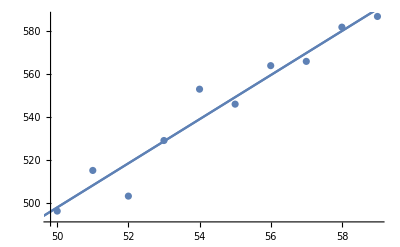

```mathematica
Clear[X,Y,sol1,sol2,x,y]
X=Table[50+i,{i,0,9}];
Y={496,515,503,529,553,546,564,566,582,587};
sol1=NMinimize[Sum[(a X[[i]]+b-Y[[i]])^2,{i,1,Length@X}],{a,b},Method->"DifferentialEvolution"]
sol2=Minimize[Sum[(a X[[i]]+b-Y[[i]])^2,{i,1,Length@X}],{a,b}]
Show[ListPlot[Transpose@{X,Y}],Plot[(a/.sol1[[2]]) x+b/.sol1[[2]],{x,48,62}],Plot[(a/.sol2[[2]]) x+b/.sol2[[2]],{x,48,62}]]
```

```mathematica
error1[a_,b_]:=Sum[(a X[[i]]+b-Y[[i]])^2,{i,1,Length@X}];
error1[9.982807066421628,0.08746479807086871]
Plot3D[Evaluate@error1[a,b],{a,-10,30},{b,-50,50}]
```

553.827

-Graphics3D-

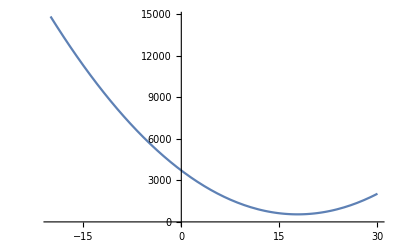

```mathematica
Plot[Sum[(10.31 X[[i]]-b-Y[[i]])^2,{i,1,Length@X}],{b,-20,30}]
```

```mathematica
logistic regression-gradient decent
```

```mathematica
X=Table[50+i,{i,0,9}];
Y={496,502,503,498,553,546,564,551,544,567};
```

```mathematica
Manipulate[Plot[1/(1+a ⅇ^(b  x+c)),{x,-15,15},PlotRange->{0,1},ImageSize->300],{a,0,2},{b,-2,2},{c,-2,2}]
```

```mathematica
Plot3D[-y Log[z]-(1-y)Log[1-z],{y,-.5,1.5},{z,0,1},PerformanceGoal->"Quality",WorkingPrecision->999,PlotRange->{0,3},AxesLabel->{y,z}]
```

-Graphics3D-

{2.41176,{b→1.35626,c→-26.5559}}

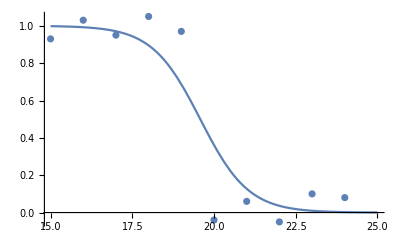

```mathematica
X=Table[x0+i,{i,0,9}];x0=15;
Y={.93,1.03,0.95,1.05,.97,-0.04,0.06,-0.05,0.1,0.08};
sig[x_]:=1/(1+ⅇ^(b x+c));
sol3=NMinimize[Sum[-Y[[i]] Log[sig[X[[i]]]]-(1-Y[[i]])Log[1-sig[X[[i]]]],{i,1,Length@X}],{b,c},Method->"DifferentialEvolution"]
Show[ListPlot[Transpose@{X,Y}],Plot[1/(1+ Exp[(b/.sol3[[2]])x+c/.sol3[[2]]]),{x,x0,x0+10}],PlotRange->All,ImageSize->400]
```

{1.47815×10^-6,{b→59.5777,c→-1135.45}}

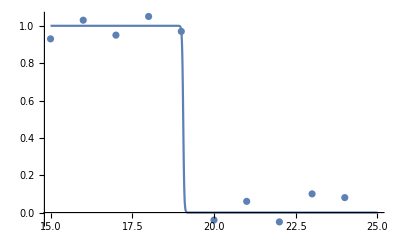

```mathematica
X=Table[x0+i,{i,0,9}];x0=15;
Y={.93,1.03,0.95,1.05,.97,-0.04,0.06,-0.05,0.1,0.08};
sig[x_]:=1/(1+ⅇ^(b x+c));
sol3=NMinimize[Sum[(Y[[i]]-sig[X[[i]]])^6,{i,1,Length@X}],{b,c},Method->"SimulatedAnnealing"]
Show[ListPlot[Transpose@{X,Y}],Plot[1/(1+ Exp[(b/.sol3[[2]])x+c/.sol3[[2]]]),{x,x0,x0+10}],PlotRange->All,ImageSize->400]
```

```mathematica
Manipulate[Plot3D[1/(1+ⅇ^(a x^2+b x+c y^2+d y+e)),{x,-5,5},{y,-5,5},PerformanceGoal->"Quality",PlotRange->All,AxesLabel->{x,y}],{a,-2,2},{b,-2,2},{c,-2,2},{d,-2,2},{e,-3,3}]
```

```mathematica
X=Table[{x0+i,x1+j},{i,0,9},{j,0,9}];x0=15;y0=10;
Y={{.93,1.03,0.95,1.05,.97,-0.04,-0.03,-0.05,0.1,0.08},{.94,1.05,0.94,0.97,0.99,-0.03,-0.04,0.02,0.03,0.08},{.98,1.01,0.98,0.99,1.03,1.01,-0.04,-0.02,-0.03,0.04},{.94,1.05,0.94,0.97,0.99,-0.03,-0.04,-0.03,0.02,-0.01},{.95,0.97,0.99,1.07,1.02,-0.04,-0.03,-0.05,0.04,-0.06},{.99,0.97,1.05,1.07,-0.02,-0.02,-0.06,-0.05,-0.1,0.06},{1.03,0.94,0.99,1.02,1.01,0.04,0.03,-0.02,-0.06,-0.06},{1.05,0.96,0.93,0.96,0.03,-0.04,-0.06,-0.05,-0.1,0.06},{1.01,1.03,0.96,0.05,0.03,-0.06,0.03,0.05,-0.02,0.03},{1.03,0.94,0.99,1.02,1.01,0.04,-0.02,-0.05,0.06,-0.06}};
sig[x_,y_]:=1/(1+ⅇ^(a x^2+b x+c y^2+d y+e));
sol3=NMinimize[Sum[(Y[[i]][[j]]-sig[X[[i]][[1]][[1]],X[[1]][[j]][[2]]])^4,{i,1,Length@X},{j,1,Length@X[[1]]}],{a,b,c,d,e},Method->"SimulatedAnnealing"]
Show[ListPointPlot3D[Flatten[Table[{X[[i]][[1]][[1]],X[[1]][[j]][[2]],Y[[i]][[j]]},{i,1,10},{j,1,10}],1]],Plot3D[1/(1+ Exp[(a/.sol3[[2]])x^2+(b/.sol3[[2]])x+(c/.sol3[[2]])y^2+(d/.sol3[[2]])y+e/.sol3[[2]]]),{x,x0,x0+10},{y,x1,y0+10}],PlotRange->All,ImageSize->400,AxesLabel->{x,y}]
```

{0.969537,{a→-0.00578456,b→0.390425,c→0.115527,d→-2.07947,e→0.788429}}

-Graphics3D-

```mathematica
Manipulate[Evaluate@Sum[-Y[[i,j]] Log[sig[X[[i]][[1]][[1]],X[[1]][[j]][[2]]]]-(1-Y[[i,j]])Log[1-sig[X[[i]][[1]][[1]],X[[1]][[j]][[2]]]],{i,1,Length@X},{j,1,Length@X[[1]]}],{a,-2,2},{b,-2,2},{c,-2,2},{d,-2,2},{e,-3,3}]
Manipulate[Evaluate@sig[X[[5]][[1]][[1]],X[[1]][[6]][[2]]],{a,-.2,.2},{b,-.2,2},{c,-.2,.2},{d,-.2,.2},{e,-.3,.3}]
Clear[a,b,c,d,e]
```

```mathematica
X=Table[{x0+i,x1+j},{i,0,9},{j,0,9}];x0=15;y0=10;
Y={{.93,1.03,0.95,1.05,.97,-0.04,-0.03,-0.05,0.1,0.08},{.94,1.05,0.94,0.97,0.99,-0.03,-0.04,0.02,0.03,0.08},{.98,1.01,0.98,0.99,1.03,1.01,-0.04,-0.02,-0.03,0.04},{.94,1.05,0.94,0.97,0.99,-0.03,-0.04,-0.03,0.02,-0.01},{.95,0.97,0.99,1.07,1.02,-0.04,-0.03,-0.05,0.04,-0.06},{.99,0.97,1.05,1.07,-0.02,-0.02,-0.06,-0.05,-0.1,0.06},{1.03,0.94,0.99,1.02,1.01,0.04,0.03,-0.02,-0.06,-0.06},{1.05,0.96,0.93,0.96,0.03,-0.04,-0.06,-0.05,-0.1,0.06},{1.01,1.03,0.96,0.05,0.03,-0.06,0.03,0.05,-0.02,0.03},{1.03,0.94,0.99,1.02,1.01,0.04,-0.02,-0.05,0.06,-0.06}};
sig[x_,y_]:=1/(1+ⅇ^(a x^2+b x+c y^2+d y+e));
sol3=NMinimize[Evaluate@Sum[-Y[[i,j]] Log[sig[X[[i]][[1]][[1]],X[[1]][[j]][[2]]]]-(1-Y[[i,j]])Log[1-sig[X[[i]][[1]][[1]],X[[1]][[j]][[2]]]],{i,1,Length@X},{j,1,Length@X[[1]]}],{a,b,c,d,e},Method->"SimulatedAnnealing"]
Show[ListPointPlot3D[Flatten[Table[{X[[i]][[1]][[1]],X[[1]][[j]][[2]],Y[[i]][[j]]},{i,1,10},{j,1,10}],1]],Plot3D[1/(1+ Exp[(a/.sol3[[2]])x^2+(b/.sol3[[2]])x+(c/.sol3[[2]])y^2+(d/.sol3[[2]])y+e/.sol3[[2]]]),{x,x0,x0+10},{y,x1,y0+10}],PlotRange->All,ImageSize->400,AxesLabel->{x,y}]
```

NMinimize::nnum: The function value Indeterminate is not a number at {a,b,c,d,e} = {-0.174933,0.817855,-0.438349,-0.0985199,0.12781}.

NMinimize[-0.93 Log[1/(1+ⅇ^(225 a+15 b+100 c+10 d+e))]-0.94 Log[1/(1+ⅇ^(256 a+16 b+100 c+10 d+e))]-0.98 Log[1/(1+ⅇ^(289 a+17 b+100 c+10 d+e))]-0.94 Log[1/(1+ⅇ^(324 a+18 b+100 c+10 d+e))]-0.95 Log[1/(1+ⅇ^(361 a+19 b+100 c+10 d+e))]-0.99 Log[1/(1+ⅇ^(400 a+20 b+100 c+10 d+e))]-1.03 Log[1/(1+ⅇ^(441 a+21 b+100 c+10 d+e))]-1.05 Log[1/(1+ⅇ^(484 a+22 b+100 c+10 d+e))]-1.01 Log[1/(1+ⅇ^(529 a+23 b+100 c+10 d+e))]-1.03 Log[1/(1+ⅇ^(576 a+24 b+100 c+10 d+e))]-1.03 Log[1/(1+ⅇ^(225 a+15 b+121 c+11 d+e))]-1.05 Log[1/(1+ⅇ^(256 a+16 b+121 c+11 d+e))]-1.01 Log[1/(1+ⅇ^(289 a+17 b+121 c+11 d+e))]-1.05 Log[1/(1+ⅇ^(324 a+18 b+121 c+11 d+e))]-0.97 Log[1/(1+ⅇ^(361 a+19 b+121 c+11 d+e))]-0.97 Log[1/(1+ⅇ^(400 a+20 b+121 c+11 d+e))]-0.94 Log[1/(1+ⅇ^(441 a+21 b+121 c+11 d+e))]-0.96 Log[1/(1+ⅇ^(484 a+22 b+121 c+11 d+e))]-1.03 Log[1/(1+ⅇ^(529 a+23 b+121 c+11 d+e))]-0.94 Log[1/(1+ⅇ^(576 a+24 b+121 c+11 d+e))]-0.95 Log[1/(1+ⅇ^(225 a+15 b+144 c+12 d+e))]-0.94 Log[1/(1+ⅇ^(256 a+16 b+144 c+12 d+e))]-0.98 Log[1/(1+ⅇ^(289 a+17 b+144 c+12 d+e))]-0.94 Log[1/(1+ⅇ^(324 a+18 b+144 c+12 d+e))]-0.99 Log[1/(1+ⅇ^(361 a+19 b+144 c+12 d+e))]-1.05 Log[1/(1+ⅇ^(400 a+20 b+144 c+12 d+e))]-0.99 Log[1/(1+ⅇ^(441 a+21 b+144 c+12 d+e))]-0.93 Log[1/(1+ⅇ^(484 a+22 b+144 c+12 d+e))]-0.96 Log[1/(1+ⅇ^(529 a+23 b+144 c+12 d+e))]-0.99 Log[1/(1+ⅇ^(576 a+24 b+144 c+12 d+e))]-1.05 Log[1/(1+ⅇ^(225 a+15 b+169 c+13 d+e))]-0.97 Log[1/(1+ⅇ^(256 a+16 b+169 c+13 d+e))]-0.99 Log[1/(1+ⅇ^(289 a+17 b+169 c+13 d+e))]-0.97 Log[1/(1+ⅇ^(324 a+18 b+169 c+13 d+e))]-1.07 Log[1/(1+ⅇ^(361 a+19 b+169 c+13 d+e))]-1.07 Log[1/(1+ⅇ^(400 a+20 b+169 c+13 d+e))]-1.02 Log[1/(1+ⅇ^(441 a+21 b+169 c+13 d+e))]-0.96 Log[1/(1+ⅇ^(484 a+22 b+169 c+13 d+e))]-0.05 Log[1/(1+ⅇ^(529 a+23 b+169 c+13 d+e))]-1.02 Log[1/(1+ⅇ^(576 a+24 b+169 c+13 d+e))]-0.97 Log[1/(1+ⅇ^(225 a+15 b+196 c+14 d+e))]-0.99 Log[1/(1+ⅇ^(256 a+16 b+196 c+14 d+e))]-1.03 Log[1/(1+ⅇ^(289 a+17 b+196 c+14 d+e))]-0.99 Log[1/(1+ⅇ^(324 a+18 b+196 c+14 d+e))]-1.02 Log[1/(1+ⅇ^(361 a+19 b+196 c+14 d+e))]+0.02 Log[1/(1+ⅇ^(400 a+20 b+196 c+14 d+e))]-1.01 Log[1/(1+ⅇ^(441 a+21 b+196 c+14 d+e))]-0.03 Log[1/(1+ⅇ^(484 a+22 b+196 c+14 d+e))]-0.03 Log[1/(1+ⅇ^(529 a+23 b+196 c+14 d+e))]-1.01 Log[1/(1+ⅇ^(576 a+24 b+196 c+14 d+e))]+0.04 Log[1/(1+ⅇ^(225 a+15 b+225 c+15 d+e))]+0.03 Log[1/(1+ⅇ^(256 a+16 b+225 c+15 d+e))]-1.01 Log[1/(1+ⅇ^(289 a+17 b+225 c+15 d+e))]+0.03 Log[1/(1+ⅇ^(324 a+18 b+225 c+15 d+e))]+0.04 Log[1/(1+ⅇ^(361 a+19 b+225 c+15 d+e))]+0.02 Log[1/(1+ⅇ^(400 a+20 b+225 c+15 d+e))]-0.04 Log[1/(1+ⅇ^(441 a+21 b+225 c+15 d+e))]+0.04 Log[1/(1+ⅇ^(484 a+22 b+225 c+15 d+e))]+0.06 Log[1/(1+ⅇ^(529 a+23 b+225 c+15 d+e))]-0.04 Log[1/(1+ⅇ^(576 a+24 b+225 c+15 d+e))]+0.03 Log[1/(1+ⅇ^(225 a+15 b+256 c+16 d+e))]+0.04 Log[1/(1+ⅇ^(256 a+16 b+256 c+16 d+e))]+0.04 Log[1/(1+ⅇ^(289 a+17 b+256 c+16 d+e))]+0.04 Log[1/(1+ⅇ^(324 a+18 b+256 c+16 d+e))]+0.03 Log[1/(1+ⅇ^(361 a+19 b+256 c+16 d+e))]+0.06 Log[1/(1+ⅇ^(400 a+20 b+256 c+16 d+e))]-0.03 Log[1/(1+ⅇ^(441 a+21 b+256 c+16 d+e))]+0.06 Log[1/(1+ⅇ^(484 a+22 b+256 c+16 d+e))]-0.03 Log[1/(1+ⅇ^(529 a+23 b+256 c+16 d+e))]+0.02 Log[1/(1+ⅇ^(576 a+24 b+256 c+16 d+e))]+0.05 Log[1/(1+ⅇ^(225 a+15 b+289 c+17 d+e))]-0.02 Log[1/(1+ⅇ^(256 a+16 b+289 c+17 d+e))]+0.02 Log[1/(1+ⅇ^(289 a+17 b+289 c+17 d+e))]+0.03 Log[1/(1+ⅇ^(324 a+18 b+289 c+17 d+e))]+0.05 Log[1/(1+ⅇ^(361 a+19 b+289 c+17 d+e))]+0.05 Log[1/(1+ⅇ^(400 a+20 b+289 c+17 d+e))]+0.02 Log[1/(1+ⅇ^(441 a+21 b+289 c+17 d+e))]+0.05 Log[1/(1+ⅇ^(484 a+22 b+289 c+17 d+e))]-0.05 Log[1/(1+ⅇ^(529 a+23 b+289 c+17 d+e))]+0.05 Log[1/(1+ⅇ^(576 a+24 b+289 c+17 d+e))]-0.1 Log[1/(1+ⅇ^(225 a+15 b+324 c+18 d+e))]-0.03 Log[1/(1+ⅇ^(256 a+16 b+324 c+18 d+e))]+0.03 Log[1/(1+ⅇ^(289 a+17 b+324 c+18 d+e))]-0.02 Log[1/(1+ⅇ^(324 a+18 b+324 c+18 d+e))]-0.04 Log[1/(1+ⅇ^(361 a+19 b+324 c+18 d+e))]+0.1 Log[1/(1+ⅇ^(400 a+20 b+324 c+18 d+e))]+0.06 Log[1/(1+ⅇ^(441 a+21 b+324 c+18 d+e))]+0.1 Log[1/(1+ⅇ^(484 a+22 b+324 c+18 d+e))]+0.02 Log[1/(1+ⅇ^(529 a+23 b+324 c+18 d+e))]-0.06 Log[1/(1+ⅇ^(576 a+24 b+324 c+18 d+e))]-0.08 Log[1/(1+ⅇ^(225 a+15 b+361 c+19 d+e))]-0.08 Log[1/(1+ⅇ^(256 a+16 b+361 c+19 d+e))]-0.04 Log[1/(1+ⅇ^(289 a+17 b+361 c+19 d+e))]+0.01 Log[1/(1+ⅇ^(324 a+18 b+361 c+19 d+e))]+0.06 Log[1/(1+ⅇ^(361 a+19 b+361 c+19 d+e))]-0.06 Log[1/(1+ⅇ^(400 a+20 b+361 c+19 d+e))]+0.06 Log[1/(1+ⅇ^(441 a+21 b+361 c+19 d+e))]-0.06 Log[1/(1+ⅇ^(484 a+22 b+361 c+19 d+e))]-0.03 Log[1/(1+ⅇ^(529 a+23 b+361 c+19 d+e))]+0.06 Log[1/(1+ⅇ^(576 a+24 b+361 c+19 d+e))]-0.07 Log[1-1/(1+ⅇ^(225 a+15 b+100 c+10 d+e))]-0.06 Log[1-1/(1+ⅇ^(256 a+16 b+100 c+10 d+e))]-0.02 Log[1-1/(1+ⅇ^(289 a+17 b+100 c+10 d+e))]-0.06 Log[1-1/(1+ⅇ^(324 a+18 b+100 c+10 d+e))]-0.05 Log[1-1/(1+ⅇ^(361 a+19 b+100 c+10 d+e))]-0.01 Log[1-1/(1+ⅇ^(400 a+20 b+100 c+10 d+e))]+0.03 Log[1-1/(1+ⅇ^(441 a+21 b+100 c+10 d+e))]+0.05 Log[1-1/(1+ⅇ^(484 a+22 b+100 c+10 d+e))]+0.01 Log[1-1/(1+ⅇ^(529 a+23 b+100 c+10 d+e))]+0.03 Log[1-1/(1+ⅇ^(576 a+24 b+100 c+10 d+e))]+0.03 Log[1-1/(1+ⅇ^(225 a+15 b+121 c+11 d+e))]+0.05 Log[1-1/(1+ⅇ^(256 a+16 b+121 c+11 d+e))]+0.01 Log[1-1/(1+ⅇ^(289 a+17 b+121 c+11 d+e))]+0.05 Log[1-1/(1+ⅇ^(324 a+18 b+121 c+11 d+e))]-0.03 Log[1-1/(1+ⅇ^(361 a+19 b+121 c+11 d+e))]-0.03 Log[1-1/(1+ⅇ^(400 a+20 b+121 c+11 d+e))]-0.06 Log[1-1/(1+ⅇ^(441 a+21 b+121 c+11 d+e))]-0.04 Log[1-1/(1+ⅇ^(484 a+22 b+121 c+11 d+e))]+0.03 Log[1-1/(1+ⅇ^(529 a+23 b+121 c+11 d+e))]-0.06 Log[1-1/(1+ⅇ^(576 a+24 b+121 c+11 d+e))]-0.05 Log[1-1/(1+ⅇ^(225 a+15 b+144 c+12 d+e))]-0.06 Log[1-1/(1+ⅇ^(256 a+16 b+144 c+12 d+e))]-0.02 Log[1-1/(1+ⅇ^(289 a+17 b+144 c+12 d+e))]-0.06 Log[1-1/(1+ⅇ^(324 a+18 b+144 c+12 d+e))]-0.01 Log[1-1/(1+ⅇ^(361 a+19 b+144 c+12 d+e))]+0.05 Log[1-1/(1+ⅇ^(400 a+20 b+144 c+12 d+e))]-0.01 Log[1-1/(1+ⅇ^(441 a+21 b+144 c+12 d+e))]-0.07 Log[1-1/(1+ⅇ^(484 a+22 b+144 c+12 d+e))]-0.04 Log[1-1/(1+ⅇ^(529 a+23 b+144 c+12 d+e))]-0.01 Log[1-1/(1+ⅇ^(576 a+24 b+144 c+12 d+e))]+0.05 Log[1-1/(1+ⅇ^(225 a+15 b+169 c+13 d+e))]-0.03 Log[1-1/(1+ⅇ^(256 a+16 b+169 c+13 d+e))]-0.01 Log[1-1/(1+ⅇ^(289 a+17 b+169 c+13 d+e))]-0.03 Log[1-1/(1+ⅇ^(324 a+18 b+169 c+13 d+e))]+0.07 Log[1-1/(1+ⅇ^(361 a+19 b+169 c+13 d+e))]+0.07 Log[1-1/(1+ⅇ^(400 a+20 b+169 c+13 d+e))]+0.02 Log[1-1/(1+ⅇ^(441 a+21 b+169 c+13 d+e))]-0.04 Log[1-1/(1+ⅇ^(484 a+22 b+169 c+13 d+e))]-0.95 Log[1-1/(1+ⅇ^(529 a+23 b+169 c+13 d+e))]+0.02 Log[1-1/(1+ⅇ^(576 a+24 b+169 c+13 d+e))]-0.03 Log[1-1/(1+ⅇ^(225 a+15 b+196 c+14 d+e))]-0.01 Log[1-1/(1+ⅇ^(256 a+16 b+196 c+14 d+e))]+0.03 Log[1-1/(1+ⅇ^(289 a+17 b+196 c+14 d+e))]-0.01 Log[1-1/(1+ⅇ^(324 a+18 b+196 c+14 d+e))]+0.02 Log[1-1/(1+ⅇ^(361 a+19 b+196 c+14 d+e))]-1.02 Log[1-1/(1+ⅇ^(400 a+20 b+196 c+14 d+e))]+0.01 Log[1-1/(1+ⅇ^(441 a+21 b+196 c+14 d+e))]-0.97 Log[1-1/(1+ⅇ^(484 a+22 b+196 c+14 d+e))]-0.97 Log[1-1/(1+ⅇ^(529 a+23 b+196 c+14 d+e))]+0.01 Log[1-1/(1+ⅇ^(576 a+24 b+196 c+14 d+e))]-1.04 Log[1-1/(1+ⅇ^(225 a+15 b+225 c+15 d+e))]-1.03 Log[1-1/(1+ⅇ^(256 a+16 b+225 c+15 d+e))]+0.01 Log[1-1/(1+ⅇ^(289 a+17 b+225 c+15 d+e))]-1.03 Log[1-1/(1+ⅇ^(324 a+18 b+225 c+15 d+e))]-1.04 Log[1-1/(1+ⅇ^(361 a+19 b+225 c+15 d+e))]-1.02 Log[1-1/(1+ⅇ^(400 a+20 b+225 c+15 d+e))]-0.96 Log[1-1/(1+ⅇ^(441 a+21 b+225 c+15 d+e))]-1.04 Log[1-1/(1+ⅇ^(484 a+22 b+225 c+15 d+e))]-1.06 Log[1-1/(1+ⅇ^(529 a+23 b+225 c+15 d+e))]-0.96 Log[1-1/(1+ⅇ^(576 a+24 b+225 c+15 d+e))]-1.03 Log[1-1/(1+ⅇ^(225 a+15 b+256 c+16 d+e))]-1.04 Log[1-1/(1+ⅇ^(256 a+16 b+256 c+16 d+e))]-1.04 Log[1-1/(1+ⅇ^(289 a+17 b+256 c+16 d+e))]-1.04 Log[1-1/(1+ⅇ^(324 a+18 b+256 c+16 d+e))]-1.03 Log[1-1/(1+ⅇ^(361 a+19 b+256 c+16 d+e))]-1.06 Log[1-1/(1+ⅇ^(400 a+20 b+256 c+16 d+e))]-0.97 Log[1-1/(1+ⅇ^(441 a+21 b+256 c+16 d+e))]-1.06 Log[1-1/(1+ⅇ^(484 a+22 b+256 c+16 d+e))]-0.97 Log[1-1/(1+ⅇ^(529 a+23 b+256 c+16 d+e))]-1.02 Log[1-1/(1+ⅇ^(576 a+24 b+256 c+16 d+e))]-1.05 Log[1-1/(1+ⅇ^(225 a+15 b+289 c+17 d+e))]-0.98 Log[1-1/(1+ⅇ^(256 a+16 b+289 c+17 d+e))]-1.02 Log[1-1/(1+ⅇ^(289 a+17 b+289 c+17 d+e))]-1.03 Log[1-1/(1+ⅇ^(324 a+18 b+289 c+17 d+e))]-1.05 Log[1-1/(1+ⅇ^(361 a+19 b+289 c+17 d+e))]-1.05 Log[1-1/(1+ⅇ^(400 a+20 b+289 c+17 d+e))]-1.02 Log[1-1/(1+ⅇ^(441 a+21 b+289 c+17 d+e))]-1.05 Log[1-1/(1+ⅇ^(484 a+22 b+289 c+17 d+e))]-0.95 Log[1-1/(1+ⅇ^(529 a+23 b+289 c+17 d+e))]-1.05 Log[1-1/(1+ⅇ^(576 a+24 b+289 c+17 d+e))]-0.9 Log[1-1/(1+ⅇ^(225 a+15 b+324 c+18 d+e))]-0.97 Log[1-1/(1+ⅇ^(256 a+16 b+324 c+18 d+e))]-1.03 Log[1-1/(1+ⅇ^(289 a+17 b+324 c+18 d+e))]-0.98 Log[1-1/(1+ⅇ^(324 a+18 b+324 c+18 d+e))]-0.96 Log[1-1/(1+ⅇ^(361 a+19 b+324 c+18 d+e))]-1.1 Log[1-1/(1+ⅇ^(400 a+20 b+324 c+18 d+e))]-1.06 Log[1-1/(1+ⅇ^(441 a+21 b+324 c+18 d+e))]-1.1 Log[1-1/(1+ⅇ^(484 a+22 b+324 c+18 d+e))]-1.02 Log[1-1/(1+ⅇ^(529 a+23 b+324 c+18 d+e))]-0.94 Log[1-1/(1+ⅇ^(576 a+24 b+324 c+18 d+e))]-0.92 Log[1-1/(1+ⅇ^(225 a+15 b+361 c+19 d+e))]-0.92 Log[1-1/(1+ⅇ^(256 a+16 b+361 c+19 d+e))]-0.96 Log[1-1/(1+ⅇ^(289 a+17 b+361 c+19 d+e))]-1.01 Log[1-1/(1+ⅇ^(324 a+18 b+361 c+19 d+e))]-1.06 Log[1-1/(1+ⅇ^(361 a+19 b+361 c+19 d+e))]-0.94 Log[1-1/(1+ⅇ^(400 a+20 b+361 c+19 d+e))]-1.06 Log[1-1/(1+ⅇ^(441 a+21 b+361 c+19 d+e))]-0.94 Log[1-1/(1+ⅇ^(484 a+22 b+361 c+19 d+e))]-0.97 Log[1-1/(1+ⅇ^(529 a+23 b+361 c+19 d+e))]-1.06 Log[1-1/(1+ⅇ^(576 a+24 b+361 c+19 d+e))],{a,b,c,d,e},Method→SimulatedAnnealing]

NMinimize::nnum: The function value Indeterminate is not a number at {a,b,c,d,e} = {-0.174933,0.817855,-0.438349,-0.0985199,0.12781}.

ReplaceAll::reps: {a,b,c,d,e} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NMinimize::nnum: The function value Indeterminate is not a number at {a,b,c,d,e} = {-0.174933,0.817855,-0.438349,-0.0985199,0.12781}.

ReplaceAll::reps: {a,b,c,d,e} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

NMinimize::nnum: The function value Indeterminate is not a number at {a,b,c,d,e} = {-0.174933,0.817855,-0.438349,-0.0985199,0.12781}.

General::stop: Further output of NMinimize::nnum will be suppressed during this calculation.

$Aborted